```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/phy456-qmII" ] 

<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 18];

(*fs = Style[#, FontSize-> 16]&;*)
```

/Users/pjoot/project/figures/phy456-qmII

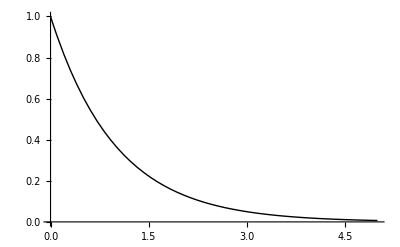

```mathematica
hydrogenGroundStateFig2 = Plot[Exp[-x], {x,0,5}, 
AxesLabel->{
(*"r/a_0" // fs, 
"Φ_100(r)" // fs*)
MaTeX["r/a_0"],
MaTeX["\\Phi_{100}(r)"]
}, 
Ticks -> None, 
PlotStyle->{Thick, Black}
]
```

```mathematica
peeters`exportForLatex["hydrogenGroundStateFig2", hydrogenGroundStateFig2]
```

{hydrogenGroundStateFig2.eps,hydrogenGroundStateFig2pn.png}

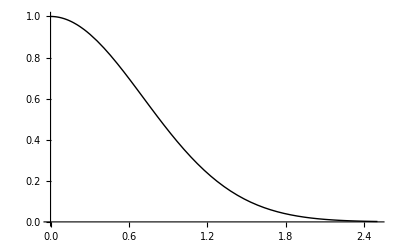

```mathematica
hydrogenGroundStateFig4 = Plot[Exp[-x^2], {x,0,2.5}, 
AxesLabel->{
(*"r" // fs, 
"ⅇ^(- α SuperscriptBox[r, 2])" // fs*)
MaTeX["r"],
MaTeX["e^{-\\alpha r^2}"]
}, 
Ticks -> None, 
PlotStyle->{Thick, Black}
]
```

```mathematica
peeters`exportForLatex["hydrogenGroundStateFig4", hydrogenGroundStateFig4]
```

{hydrogenGroundStateFig4.eps,hydrogenGroundStateFig4pn.png}

```mathematica
nike[a_] := Plot[ 
{Callout[x - a Sqrt[x], "\\alpha_0" // MaTeX, Below],
x - a Sqrt[x]}, {x,0,2}, 
Ticks -> None, 
PlotStyle-> {Thick, Black},
AxesLabel->{
(*"α" // fs, 
"E(α)" // fs*)
MaTeX["\\alpha"],
MaTeX["E(\\alpha)"]
}
]
Manipulate[ nike[a],
{{a,1.2},0,2}]
hydrogenGroundStateFig5 = nike[1.2]
```

-Graphics-

```mathematica
peeters`exportForLatex["hydrogenGroundStateFig5", hydrogenGroundStateFig5]
```

{hydrogenGroundStateFig5.eps,hydrogenGroundStateFig5pn.png}